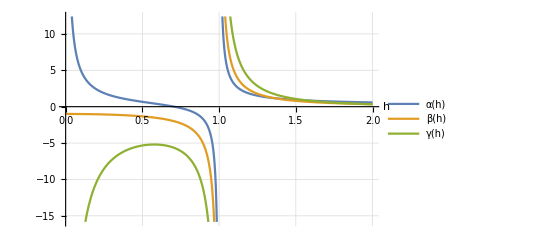

```mathematica
(*α[h_]:=(0.5 / h) (2 - h^2) / (4-h^2);
β[h_] := 0.5 / (4-h^2);
γ[h_] := -1 / (h(4-h^2));*)

α[h_]:=(1 / h) (1/2 - 3h^2/2+h^4) / (1-h^2)^2;
β[h_] := -1 / (1-h^2);
γ[h_] := -2 / (h(1-h^2));

plot =Plot[{α[h], β[h], γ[h]}, {h, 0, 2}, GridLines->Automatic, AxesLabel->{h, None},BaseStyle->{FontSize->18}, PlotLegends->"Expressions", TicksStyle->Directive[ 12]]
```